NDSolve::nderr: Error test failure at x == 0.11013071031210107730675348756339451809301926722655815637380390732513102451767333; unable to continue.

{{ω[x]→InterpolatingFunction[{{0.11013071031210107730675348756339451809301926722655815637380390732513102451767333, 0.47958315233127195415974380641626939199967070419041293464853091144482572359074641}}, <>][x],z[x]→InterpolatingFunction[{{0.11013071031210107730675348756339451809301926722655815637380390732513102451767333, 0.47958315233127195415974380641626939199967070419041293464853091144482572359074641}}, <>][x]}}

InterpolatingFunction::dmval: Input value {0.000100017} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

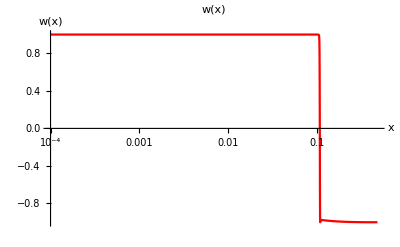

For ω(x₀) = ω[(√23)/10] and dω/dx(x₀) = ω'[(√23)/10], the ratio Ω_Λ / Ω_M is: 1/23

```mathematica
ClearAll[ω,z]

ΩM=23/100;λ=1/100;x1=ΩM^(1/2);
(*V0=8 π G;*)
ΩFinal=1-ΩM;
dΩFinal=0;
zFinal=0;
Hubble[ω_,dωdx_,z_]:=Sqrt[(1+z)^3+ω+(1/(2 λ)) (dωdx)^2]


eq1=ω''[x]+3 Hubble[ω[x],ω'[x],z[x]] ω'[x]+λ==0;eq2=z'[x]==-Hubble[ω[x],ω'[x],z[x]] (1+z[x]);initialConditions={ω[x1]==ΩFinal,ω'[x1]==dΩFinal,z[x1]==zFinal};


xi=10^-4;
ClearAll[ω,z]
backwardSolution=NDSolve[{eq1,eq2,initialConditions},{ω[x],z[x]},{x,x1,xi},WorkingPrecision->80,MaxSteps->20000]

ωSolutionBackward=ω[x]/.backwardSolution[[1]];
zSolutionBackward=z[x]/.backwardSolution[[1]];


w[x_]=((D[ω[x]/.backwardSolution[[1]],x])^2-(2 λ ω[x]//.backwardSolution[[1]]))/((D[ω[x]/.backwardSolution[[1]],x])^2+(2 λ ω[x]//.backwardSolution[[1]]));


LogLinearPlot[w[x],{x,x1,xi},PlotLabel->"w(x)",AxesLabel->{"x","w(x)"},PlotRange->All,PlotStyle->Red]

Print["For ω(x₀) = ",ω[x1]/.backwardSolution[[1]]," and dω/dx(x₀) = ",ω'[x1]/.backwardSolution[[1]],", the ratio Ω_Λ / Ω_M is: ",λ/ΩM];
```

```mathematica
3
```

3

```mathematica
6
```

6

```mathematica
(* Heat Map *)
λ=0.1;
OmegaRatio[ω0_,dωdx0_]:=ω0+(1/(2 λ)) (dωdx0^2)

ΩRange=Range[0,2,0.001];

dΩdxRange=Range[-2,2,0.001];

spectrumMatrix=Table[OmegaRatio[ω0,dωdx0],{ω0,ΩRange},{dωdx0,dΩdxRange}];


MatrixPlot[spectrumMatrix,ColorFunction->"TemperatureMap",Frame->True,FrameLabel->{"ω(x₀)","dω/dx(x₀)"},PlotLabel->"Heatmap of Ω_Λ / Ω_M",Mesh->False,ColorFunctionScaling->True]
```

-Graphics-

InterpolatingFunction::dmval: Input value {0.000109795} lies outside the range of data in the interpolating function. Extrapolation will be used.

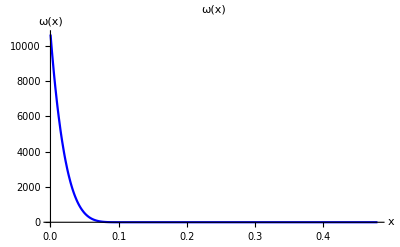

InterpolatingFunction::dmval: Input value {0.000109795} lies outside the range of data in the interpolating function. Extrapolation will be used.

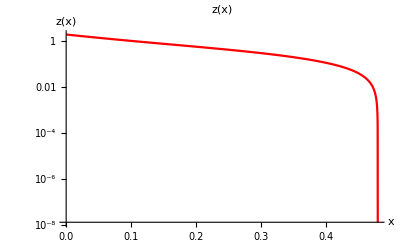

```mathematica
(*Plot ω(x) over x*)Plot[ωSolutionBackward,{x,xi,x1},PlotLabel->"ω(x)",AxesLabel->{"x","ω(x)"},PlotRange->All,PlotStyle->Blue]

(*Plot z(x) over x*)
LogPlot[zSolutionBackward,{x,xi,x1},PlotLabel->"z(x)",AxesLabel->{"x","z(x)"},PlotRange->All,PlotStyle->Red]
```

InterpolatingFunction::dmval: Input value {0.000109795} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

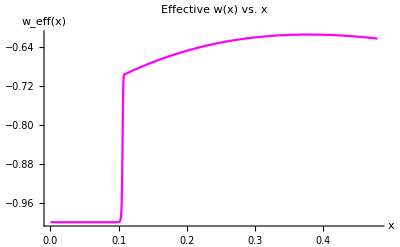

```mathematica
wEff[x_]:=-1+(2/3) ((1+z[x]/.backwardSolution[[1]])^2/Hubble[ω[x]/.backwardSolution[[1]],D[ω[x]/.backwardSolution[[1]],x],z[x]/.backwardSolution[[1]]]^2);
Plot[Evaluate[wEff[x]],{x,x1,xi},PlotLabel->"Effective w(x) vs. x",AxesLabel->{"x","w_eff(x)"},PlotRange->All,PlotStyle->Magenta]
```

InterpolatingFunction::dmval: Input value {0.000109795} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

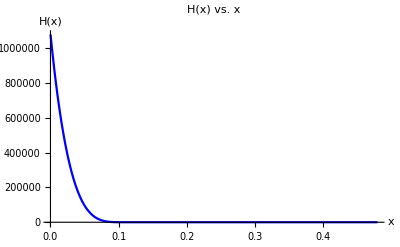

```mathematica
hubbleFunction[x_]:=Sqrt[(1+(z[x]/.backwardSolution[[1]]))^3+(ω[x]/.backwardSolution[[1]])+(1/(2 λ)) (D[ω[x]/.backwardSolution[[1]],x])^2];


Plot[Evaluate[hubbleFunction[x]],{x,x1,xi},PlotLabel->"H(x) vs. x",AxesLabel->{"x","H(x)"},PlotRange->All,PlotStyle->Blue,BaseStyle->{FontSize->14}]
```